```mathematica
dist = 26
```

26

```mathematica
func =E^(-(x-40)^2/250)
```

ⅇ^(-1/250 (-40+x)^2)

```mathematica
f1 = E^(-(x-40-dist)^2/250)
```

ⅇ^(-1/250 (-66+x)^2)

```mathematica
f2 = E^(-(x-40-2dist)^2/250)
```

ⅇ^(-1/250 (-92+x)^2)

```mathematica
f3 = E^(-(x-40-3dist)^2/250)
```

ⅇ^(-1/250 (-118+x)^2)

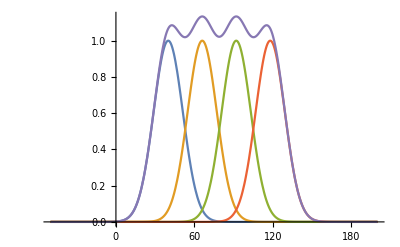

```mathematica
Plot[{func,f1,f2,f3, func+f1+f2+f3}, {x,-50,200}, PlotRange->All]
```

```mathematica
fu1= E^((-(x-40)^2)/250)
```

ⅇ^(-1/250 (-40+x)^2)

```mathematica
fu'= fu[x]
```

fu[x]

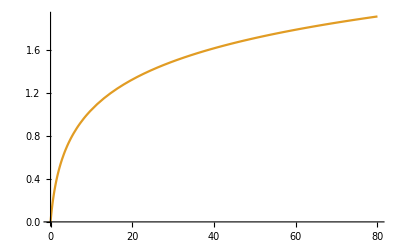

```mathematica
Plot[{fu,fu2},{x,0,80}]
```

```mathematica
Clear[function]
```

```mathematica
function[p_/;p>0] := 180*(E^(-0.25p)−E^(−0.6p))
```

```mathematica
function[p_/;p≤ 0]:= 0
```

```mathematica
function[x+25]
```

function[25+x]

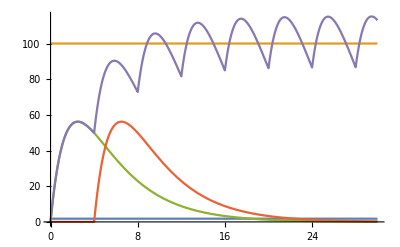

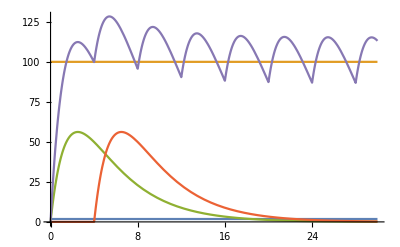

```mathematica
Plot[{1.8,100,
function[x],function[x-4],
function[x]+function[x-4]+function[x-8]+function[x-12]+
function[x-16]+function[x-20]+function[x-24]+function[x-28]
},
{x,0,30}, PlotRange-> Automatic]
```

```mathematica
test = E^(-x/20) - E^(-(x/15))
```

-ⅇ^(-x/15)+ⅇ^(-x/20)

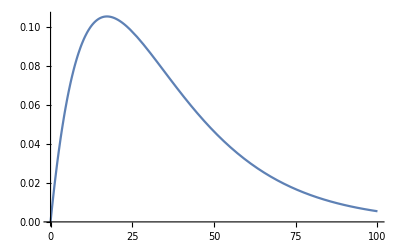

```mathematica
Plot[test,{x,0,100}]
```

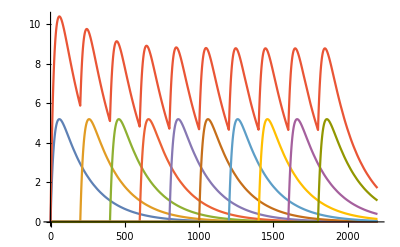

```mathematica
Clear[y];
k=200;
r=25;
interval =-200;
y[x_/;x>0]:=(k/r)(E^(-x/(k))-E^(-x/r));
y[x_/;x≤ 0]:= 0;
Plot[{y[x],y[x+interval],y[x+2interval],y[x+3interval],y[x+4interval],y[x+5interval],y[x+6interval],y[x+7interval],y[x+8interval],y[x+9interval],
y[x]*2+y[x+interval]+y[x+2interval]+y[x+3interval]+y[x+4interval]+y[x+5interval]+y[x+6interval]+y[x+7interval]+y[x+8interval]+y[x+9interval]
},{x,0,11*-interval}, PlotRange-> All]
```

```mathematica
Plot[y[x],y[x+interval],y[x+2interval],y[x+3interval],y[x+4interval],{{y[x+5interval], y[x+6interval],y[x+7interval],y[x+8interval],y[x+9interval],y[x+10interval]}},{x,-1,100},PlotRange->All]
```

```mathematica
Clear[y];
Clear[k]; 
Clear[t];
Clear[r];
solved =DSolve[{y'[t]==k-r y[t]},y[t],t]
```

{{y[t]→k/r+ⅇ^(-r t) C[1]}}

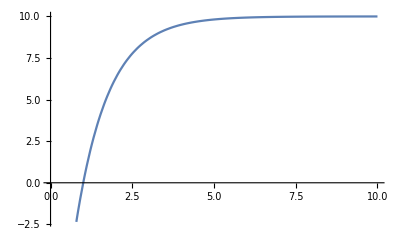

```mathematica
Plot[10-10*E^-(x-1),{x,0,10}]
```